## Cross protection and blunting

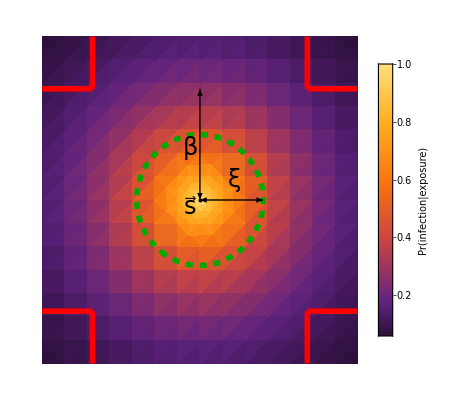

```mathematica
crossprotectionplot=
Legended[
Show[
DensityPlot[N[Exp[-Sqrt[x^2+y^2]/1.25]],{x,-2.5,2.5},{y,-2.5,2.5},ColorFunction->Function[z,ColorData["SunsetColors"][0.75*(z+.1)]], 
PlotLegends->
Placed[
BarLegend[
Automatic,
LegendMarkerSize->382,
LegendMargins->{{0,0},{-10,0}},
LabelStyle->{FontSize->24, Black},
LegendLabel->Placed[Style["Pr(infection|exposure)",24,Black],Right,Rotate[#,-90 Degree] &]
],Right
],
Frame->None],
ContourPlot[Exp[-√(x^2+y^2)],{x,-2.5,2.5},{y,-2.5,2.5}, Contours->{Exp[-1]}, ContourShading->None, ContourStyle->Directive[Darker[Green],Dashed, Thickness[.01]]],
Graphics[{Transparent,EdgeForm[{Thickness[0.01],Blue}],Rectangle[{-1.7,1.7},{1.7,-1.7}]}],
Graphics[{Thickness[.01],Red, Line[{{-2.5,-1.7},{-1.7,-1.7}}]}],

Graphics[{Thickness[.01],Red, Line[{{-1.7,-2.5},{-1.7,-1.7}}]}],

Graphics[{Thickness[.01], Red, Line[{{-2.5,1.7},{-1.7,1.7}}]}],

Graphics[{Thickness[.01],Red, Line[{{-1.7,1.7},{-1.7,2.5}}]}],

Graphics[{Thickness[.01],Red, Line[{{1.7,1.7},{1.7,2.5}}]}],

Graphics[{Thickness[.01], Red, Line[{{1.7,1.7},{2.5,1.7}}]}],

Graphics[{Thickness[.01], Red, Line[{{1.7,-2.5},{1.7,-1.7}}]}],
Graphics[{Thickness[.01], Red, Line[{{1.7,-1.7},{2.5,-1.7}}]}],
Graphics[Disk[{0,0},.03]], 
Graphics[Text[Style[OverVector[s],FontSize->24],{-.15,-.1}]],
Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,0},{1,0}}]}],
Graphics[Text[Style["ξ",FontSize->24],{0.55,0.3}]],
Graphics[{Arrowheads[{-.03,.03}],Arrow[{{0,0},{0,1.7}}]}],
Graphics[Text[Style["β",FontSize->24],{-0.15,.8}]],
Graphics[{Arrowheads[{-.03,.03}],Arrow[{{-1.7,-2.8},{1.7,-2.8}}]}]
],
Placed[LineLegend[{Directive[Thickness[.01],Red],Directive[Thickness[0.01],Blue], Directive[Dashed,Darker[Green],Thickness[.01]] },{"every-epitope","any-epitope","cross-protection"},LabelStyle->{FontSize->24}],{Below,Left}]
]
```